Replacement of the constants used in the experiment

```mathematica
rep={m->ChemicalFormula["NaCs"]["MolecularMass"],ℏ->Quantity[, "ReducedPlanckConstant"],h->Quantity[, "PlanckConstant"],U0->h Quantity[1, "Megahertz"],W0->1.15 λ,λ->Quantity[1064, "Nanometers"]};
c0=(U0 m W0^2)/ℏ^2//.rep;
d0=ℏ/(W0 √(m U0))//.rep;
dimless={x->χ ux,z->ζ ux};
```

Spatial and time used in this problem

```mathematica
ux=W0;
```

Tweezer potential

```mathematica
z0=(π W0^2)/λ;
W=W0 √(1+(z/z0)^2);
intensity=2ϵ0 c U0/Re[α] (W0/W)^2 Exp[-(2 x^2)/W^2];

U=U0-1/(2ϵ0 c)Re[α]intensity/.dimless/.ζ->0;
```

Trap frequency

```mathematica
ωx=ω/.Solve[m ω^2==(2/x^2 Normal[Series[U,{χ,0,2}]]/.dimless)&&ω>0,ω,Assumptions->{ℏ>0,c>0,U0>0,W0>0,m>0,λ>0}][[1]];
```

Time scale

```mathematica
ut=1/ωx;
```

Eigenstates

```mathematica
ψn[n_]:=1/(√(2^n n!))((m ω0)/(π ℏ))^(1/4)Exp[-(m ω0 x^2)/(2ℏ)]HermiteH[n,√((m ω0)/ℏ)x]/.dimless/.{ω0->ωx}
```

```mathematica
ψn[0]/.m √(U0/m)->ℏ/(W0 d)
```

ⅇ^(-χ^2/d) (2/π)^(1/4) (1/(d W0^2))^(1/4)

Schrodinger equation

```mathematica
U/.ζ->0
```

U0-ⅇ^(-2 χ^2) U0

### test

```mathematica
SE=FullSimplify[FullSimplify[(ⅈ D[#,τ]+(ut ℏ)/(2m ux^2)D[#,χ,χ]-ut (U +0.1U Cos[1/(2π)ωx τ ut]/.ζ->0)/ℏ#)&[ψ[χ,τ]]==0]/.√(U0/m)->(d W0 U0)/ℏ]/.(U0 m W0^2)/ℏ^2->c
```

c d (10.+1. Cos[τ/(2 π)]) Sinh[χ^2] ψ[χ,τ]+ⅇ^(χ^2) ((0.-10. ⅈ) ψ^(0,1)[χ,τ]-2.5 d ψ^(2,0)[χ,τ])==0

```mathematica
ϕ[χ_]=FullSimplify[(ψn[0]/.m √(U0/m)->ℏ/(W0 d))√ux,Assumptions->{W0>0,c>0,ℏ>0,m>0}]
```

(1/d)^(1/4) ⅇ^(-χ^2/d) (2/π)^(1/4)

NDSolve

```mathematica
SE/.{c->c0,d->d0}
```

151.961 (10.+1. Cos[τ/(2 π)]) Sinh[χ^2] ψ[χ,τ]+ⅇ^(χ^2) ((0.-10. ⅈ) ψ^(0,1)[χ,τ]-0.0164516 ψ^(2,0)[χ,τ])==0

```mathematica
xmax=1;tmax=100;
sol=NDSolve[{(SE/.{c->c0,d->d0}),ψ[χ,0]==ϕ[χ]/.d->d0,ψ[xmax,τ]==0,ψ[-xmax,τ]==0},ψ,{χ,-xmax,xmax},{τ,0,tmax}];
```

```mathematica
solution=ψ/. sol[[1]];
```

```mathematica
Manipulate[Plot[Abs[solution[x,t]]^2,{x,-xmax,xmax},PlotRange->{0,Abs[solution[0,0]]^2},Filling->{1->Axis}],{t,0,tmax}]
```

```mathematica
ωx ut//.rep
```

1

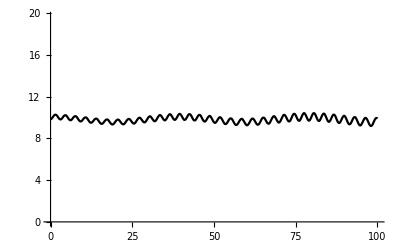

```mathematica
Plot[Abs[solution[0,t]]^2,{t,0,tmax},PlotRange->{0,2 Abs[solution[0,0]]^2},PlotStyle->Black]
```

## ND

```mathematica
ω=.;ℏ=1;U0=4;ω0=1;ω[t_]=ω0+.01 Cos[1 ω0 t];m=1;a=1;
```

```mathematica
p=-ⅈ ℏ D[#,x]&;
H=(p[p[#]]/(2m)+U0(1-ⅇ^(-(1/2 m ω[t]^2)/U0 x^2))#)&;
(*H=(p[p[#]]/(2m)+1/2 m ω[t]^2 x^2#)&;*)
```

```mathematica
SE=ⅈ D[ψ[x,t],t]==H[ψ[x,t]]/ℏ;
```

```mathematica
ψeig[n_,x_]:=1/(√(2^n n!))((m a ω0)/(π ℏ))^(1/4)Exp[-(m a ω0 x^2)/(2ℏ)]HermiteH[n,√((m a ω0)/ℏ)x]
```

```mathematica
SE
```

ⅈ ψ^(0,1)[x,t]==4 (1-ⅇ^(-1/8 x^2 (1+0.01 Cos[t])^2)) ψ[x,t]-1/2 ψ^(2,0)[x,t]

```mathematica
xmax=10;tmax=200;
schrodingerEq=-(1/2) D[ψ[x,t],{x,2}]+(1/2) x^2 ψ[x,t]==I D[ψ[x,t],t];
ψinit[x_]:=(1/π)^(1/4) Exp[-1/2 (x-1)^2];
sol=NDSolve[{SE,ψ[x,0]==ψeig[0,x],ψ[xmax,t]==0,ψ[-xmax,t]==0},ψ,{x,-xmax,xmax},{t,0,tmax},PrecisionGoal->10];
solution=ψ/. sol[[1]];
```

```mathematica
Manipulate[Plot[{Abs[solution[x,0]]^2,Abs[solution[x,t]]^2,U0(1-ⅇ^(-1/2(m ω0^2)/U0 x^2)),1/2 m ω0^2 x^2},{x,-xmax,xmax},PlotRange->{0,1},PlotStyle->{Dotted,Blue,Red,Purple},Filling->{2->Axis}],{t,0,tmax}]
```

Plot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

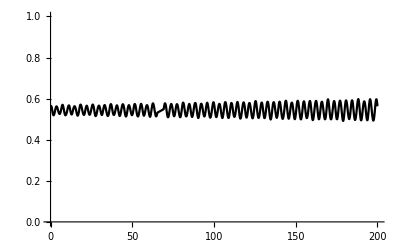

```mathematica
Plot[Abs[solution[0,t]]^2,{t,0,tmax},PlotRange->{0,1},PlotStyle->Black]
```